# Algorithm Overview

Trust region algorithms minimize f(x) by advancing from
	x_k→x_(k+1)=x_k+p
where p minimizes a typically quadratic model function 
	m[p]=g.p+0.5 p.A.p∼f[x_k+p]
 with g≈∇f(x_k) and A≈∇^2 f(x_k) over some trust region √(p.B.p)≤Δ.   Importantly if 
	f≈f(x_k)+g.p+0.5 p.A.p  for √(p.B.p)≤Δ 
and we find a reasonable solution of the TRS problem then x_(k+1) will improve on x_k.

Line-search algorithms choose a single direction p_k at x_k and looks for scalars α>0 for which 
	x_(k+1)=x_k+α p_k
improves x_k.  As before g≈∇f(x_k) and possibly A≈∇^2 f(x_k).  It is critical that p_k points downhill i.e.
	∇f(x_k).p_k<0.
Steepest descent is simply p_k=-∇f(x_k).  Newton like methods choose 
	p_k=-A^-1g
Unfortunately unless A is SPD this is a saddle.   Line search methods all need SPD A which is not great if ∇^2 f(x_k) is not SPD.

# TRS Subproblem

We can make pictures of the TRS SubProblem in 2D and 3D
	argmin_(√(p.B.p)≤Δ)g.p+0.5p.A.p
Remember B and A are symmetric n×n matrices and B is positive definite.   Just a reminder this is a generic quadratic at p=0 with a generic ellipse centered at p=0.

## n=2

### n=2: Saddle

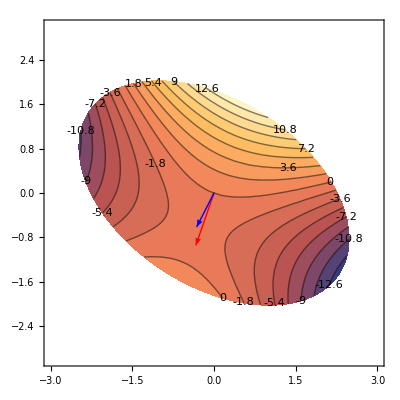

```mathematica
A={{-2.0,3},{3,4}};g={1.2,3.4};
B={{2,1},{1,3}}; Δ=3.2;
f[p_]:=0.5 p.A.p+g.p
ContourPlot[f[{p1,p2}],{p1,-3,3},{p2,-3,3},
Contours->40,
ContourLabels->All,
Epilog->{
{Red, Arrow[{{0,0},-Normalize[g]}]},
{Blue,Arrow[{{0,0},-LinearSolve[A,g]}]}
},
RegionFunction->Function[{p1,p2},{p1,p2}.B.{p1,p2}≤Δ^2]]
```

### n=2: Interior Max

```mathematica
A={{-2.0,1},{1,-2}};g={0.2,1.4};
B={{2,1},{1,3}}; Δ=3.2;
f[p_]:=0.5 p.A.p+g.p
ContourPlot[f[{p1,p2}],{p1,-3,3},{p2,-3,3},
Contours->40,
ContourLabels->All,
Epilog->{
{Red, Arrow[{{0,0},-Normalize[g]}]},
{Blue,Arrow[{{0,0},-LinearSolve[A,g]}]}
},
RegionFunction->Function[{p1,p2},{p1,p2}.B.{p1,p2}≤Δ^2]]
```

### n=2: Interior Min

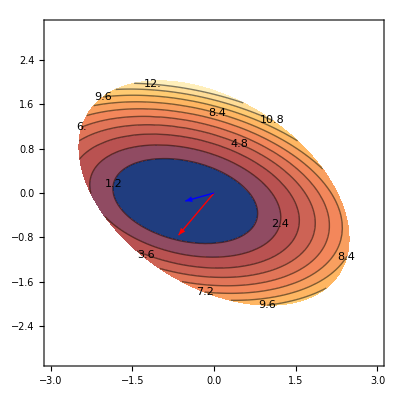

```mathematica
A={{2.0,1},{1,6}};g={1.2,1.4};
B={{2,1},{1,3}}; Δ=3.2;
f[p_]:=0.5 p.A.p+g.p
ContourPlot[f[{p1,p2}],{p1,-3,3},{p2,-3,3},
Contours->40,
ContourLabels->All,
Epilog->{
{Red, Arrow[{{0,0},-Normalize[g]}]},
{Blue,Arrow[{{0,0},-LinearSolve[A,g]}]}
},
RegionFunction->Function[{p1,p2},{p1,p2}.B.{p1,p2}≤Δ^2]]
```

## n=3

### n=3: Exterior Saddle

```mathematica
A=({{-2.0, 3, 1}, {3, 4, 2}, {1, 2, -12}});g={1.2,3.4,4};
B=({{5.0, 0, 1}, {0, 2, 0}, {1, 0, 4}}); Δ=1.1;
f[p_]:=0.5 p.A.p+g.p
Show[
ContourPlot3D[f[{p1,p2,p3}],{p1,-1,1},{p2,-1,1},{p3,-1,1},
Contours->40,
ContourStyle->Opacity[0.5],
PlotLegends->Automatic,
RegionFunction->Function[{p1,p2,p3},{p1,p2,p3}.B.{p1,p2,p3}≤Δ^2]],
Graphics3D[{Thickness[0.01],
{Red, Arrow[{{0,0,0},-Normalize[g]}]},
{Blue,Arrow[{{0,0,0},-LinearSolve[A,g]}]}
}],
PlotLabel->{Eigenvalues[A],Eigenvalues[B]}
]
```

-Graphics3D-

### n=3: Interior Saddle

```mathematica
A=({{-2.0, 3, 1}, {3, 4, 2}, {1, 2, -12}});g={0.2,1.4,0.2};
B=({{5.0, 0, 1}, {0, 2, 0}, {1, 0, 4}}); Δ=1.1;
f[p_]:=0.5 p.A.p+g.p
Show[
ContourPlot3D[f[{p1,p2,p3}],{p1,-1,1},{p2,-1,1},{p3,-1,1},
Contours->40,
ContourStyle->Opacity[0.5],
PlotLegends->Automatic,
RegionFunction->Function[{p1,p2,p3},{p1,p2,p3}.B.{p1,p2,p3}≤Δ^2]],
Graphics3D[{Thickness[0.01],
{Red, Arrow[{{0,0,0},-Normalize[g]}]},
{Blue,Arrow[{{0,0,0},-LinearSolve[A,g]}]}
}],
PlotLabel->{Eigenvalues[A],Eigenvalues[B]}
]
```

-Graphics3D-

### n=3: Exterior Min

```mathematica
A=({{2.0, 1, 1}, {1, 4, 2}, {1, 2, 12}});g={0.2,-0.4,1.1};
B=({{5.0, 0, 1}, {0, 2, 0}, {1, 0, 4}}); Δ=1.1;
f[p_]:=0.5 p.A.p+g.p
Show[
ContourPlot3D[f[{p1,p2,p3}],{p1,-1,1},{p2,-1,1},{p3,-1,1},
Contours->40,
ContourStyle->Opacity[0.5],
PlotLegends->Automatic,
RegionFunction->Function[{p1,p2,p3},{p1,p2,p3}.B.{p1,p2,p3}≤Δ^2]],
Graphics3D[{Thickness[0.01],
{Red, Arrow[{{0,0,0},-Normalize[g]}]},
{Blue,Arrow[{{0,0,0},-LinearSolve[A,g]}]}
}],
PlotLabel->{Eigenvalues[A],Eigenvalues[B]}
]
```

-Graphics3D-